#### import the data

```mathematica
importdata=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data.csv"];
data1=Values[Normal[importdata]]⟦All,Range[76]+1⟧;
```

```mathematica
Length[data1⟦All,{1,2,76}⟧]
```

176

#### classification

randomize data for training/test split

```mathematica
SeedRandom[123];
rs=RandomSample[data1⟦All,{1,2,76}⟧,176];
```

Split data into 70% training and 30% test

```mathematica
trainingset=rs⟦1;;123⟧;
testset=rs⟦124;;176⟧;
```

```mathematica
c=Classify[trainingset->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

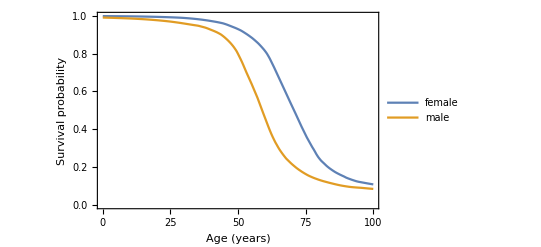

```mathematica
p[age_,gender_]:=c[{age,gender},{"Probability","survived"}];
Plot[{p[x,"female"],p[x,"male"]}, {x,0,100},PlotLegends->{"female","male"}, Frame->True,FrameLabel-> {"Age (years)", "Survival probability"}, Exclusions->None]
```

Accuracy and Confusion Matrix

```mathematica
cm=ClassifierMeasurements[c,testset->3]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.792453

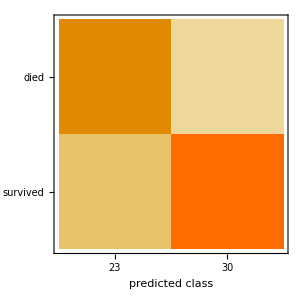

```mathematica
cm["ConfusionMatrixPlot"]
```